# Report Project X

Course code: IX12500
Date: 2018-09-14

Michel Ouadria, ouadria@kth.se
Rikard Jakobsson, rikjak@kth.se

Task 1: Probability Experiment

## Summery

### Task

Assume that you play a variant of a poker game with five cards that is using a subset of two ordinary deck of cards. The subset considered is cards valued 9,10,J,Q,K,A from the two decks, in total 48 cards.

Calculate the exact probability of the following hands using the  census method.

If a given hand contains different valued hands only one (the highest rank) is considered.

One pair

Two pairs

Three of a kind

Four of a kind

Five of a kind

Full hand

Straight

Flush

Straight flush

Nothing

### Result

●Straight Flush:
	• 256
	• 0.0149506%

●Straight:
	• 65 280
	• 3.81241%

●Full House:
	• 47 040
	• 2.74718%
	
●Five of a kind:
	• 336
	• 0.0196227%
	
●Four of a kind:
	• 16 800
	• 0.981134%
	
●Flush:
	• 2912
	• 0.170063%
	
●Three of a kind:
	• 215 040
	• 12.5585%
	
●Two pairs:
	• 37 5840
	• 21.9494%
	
●One pair:
	• 85 8240
	• 50.1219%
	
●Nothing:
	• 130 560
	• 50.1219%

### Discussion

## Road Construction?????????

### Model for cross section area

The data is interpolated as a function A(x).

### Model for volume

The requested volume to be transported can be calculated numerically with the integral

I.e. about 0.1 km^3 must be transported.

### Code

```mathematica
Quit[];
```

```mathematica
deck = {109,109,110,110,111,111,112,112,113,113,114,114,209,209,210,210,211,211,212,212,213,213,214,214,309, 309,310,310,311,
311,312,312,313,313,314,314,409,409,410,410,411,411,412,412,
413,413,414,414};

hand = Subsets[deck,{5}](*Sort deck with all subsets containing 5*)
sizeOfPermutations = Length[hand] (*Amount of different possible hands*)
```

{{109,109,110,110,111},{109,109,110,110,111},{109,109,110,110,112},{109,109,110,110,112},{109,109,110,110,113},{109,109,110,110,113},{109,109,110,110,114},1712291,{412,412,413,413,414},{412,412,413,413,414},{412,412,413,414,414},{412,412,413,414,414},{412,413,413,414,414},{412,413,413,414,414}}
 |  |  |  |

1712304

#### Straight flush

```mathematica
straightFlushQ[h_]:=MatchQ[h-h[[1]],{0,1,2,3,4}]
straightFlush =Count[hand, _?(straightFlushQ)]
N[straightFlush/sizeOfPermutations]*100
```

256

0.0149506

#### Straight

```mathematica
straightQ[{9,10,11,12,13}]:=True;(*All possible hands from 9 to K = True*)
straightQ[{10,11,12,13,14}]:=True;(*All possible hands from 10 to A = True *)
straightQ[{___}]:=False(*All other possibilities = False*)
straightRemoveSuiteQ[hand_]:= straightQ[Sort[Mod[hand,100]]]; (*Calculating suites by removing the first digit from all cards in the deck, i.e 109 = 9 ...*)
straight =(Count[hand,_?(straightRemoveSuiteQ)]-straightFlush) (*Final result of all the chances of getting straight. Subtract Straight flush since the cases above doesn't exclude it as a possibility*)
N[(straight)/sizeOfPermutations]*100 (*Probability*)
```

65280

3.81241

#### Full house

```mathematica
fullHouseQ[{x_,x_,x_,y_,y_}/;x≠y]:=True;(*Check for three of a kind and a pair, they can't be the same rank!!!!!!!!!*)
fullHouseQ[{x_,x_,y_,y_,y_}/;x≠y]:=True;(*Second scenario*)
fullHouseQ[___]:=False;(*Everything else is excluded*)
fullHouseRemoveSuiteQ[hand_]:=fullHouseQ[Sort[Mod[hand,100]]]
fullHouse =Count[hand,_?(fullHouseRemoveSuiteQ)]
N[fullHouse/sizeOfPermutations]*100
```

47040

2.74718

#### Five of a kind

```mathematica
fiveOfAKindQ[{x_,x_,x_,x_,x_}]:=True;(*Check for five of a kind*)
fiveOfAKindQ[{___}]:=False;(*Exclude everything else*)
fiveOfAKindRemoveSuiteQ[hand_]:=fiveOfAKindQ[Sort[Mod[hand,100]]]
fioak = Count[hand,_?(fiveOfAKindRemoveSuiteQ)]
N[fioak/sizeOfPermutations]*100
```

336

0.0196227

#### Four of a kind

```mathematica
fourOfAKindQ[{x_,x_,x_,x_,y_}/;x≠y]:=True; 
fourOfAKindQ[{y_,x_,x_,x_,x_}/;x≠y]:=True; 
fourOfAKindQ[{___}]:=False;
fourOfAKindRemoveSuiteQ[hand_]:=fourOfAKindQ[Sort[Mod[hand,100]]];
foak = Count[hand,_?(fourOfAKindRemoveSuiteQ)]
N[foak/sizeOfPermutations]*100
```

16800

0.981134

#### Flush

```mathematica
flushQ[h_]:=MatchQ[(h-h[[1] ]),{0,0,0,0,0}](**)
flushGetSuiteQ[hand_]:= flushQ[Quotient[hand,100]](*Get the suite through quotienet function. I.e 109 = 100!!!!!!!*)
flush=Count[hand,_?(flushGetSuiteQ)]- straightFlush
N[flush/sizeOfPermutations]*100
```

2912

0.170063

#### Three of a kind

```mathematica
threeOfAKindQ[{___,x_,x_,x_,x_,___}]:=False; (*Four of a kind excluded*)
threeOfAKindQ[{x_,x_,y_,y_,y_}/;x≠y]:=False;(*Full house excluded*)
threeOfAKindQ[{x_,x_,x_,y_,y_}/;x≠y]:=False;(*Second scenario of full house*)
threeOfAKindQ[{___,x_,x_,x_,___}]:=True; (*Three of a kind*)
threeOfAKindQ[{___}]:=False; 
threeOfAKindRemoveSuiteQ[hand_]:=threeOfAKindQ[Sort[Mod[hand,100]]];
threePair =Count[hand,_?(threeOfAKindRemoveSuiteQ)]
N[threePair/sizeOfPermutations]*100
```

215040

12.5585

#### Two Pair Flush

```mathematica
twoPairQ[{x_,x_,y_,y_,z_}/;x≠y≠z]:=True;(*Two pair*)
twoPairQ[{z_,x_,x_,y_,y_}/;x≠y≠z]:=True;(*Second scenario*)
twoPairQ[{x_,x_,z_,y_,y_}/;x≠y≠z]:=True;(*Third senarioa*)
twoPairQ[{___}]:=False;
twoPairRemoveSuiteQ[hand_]:=twoPairQ[Sort[Mod[hand,100]]];
(**)
twoPairWithFlushQ[hand_]:=twoPairRemoveSuiteQ[hand]&&flushGetSuiteQ[hand]
twoPairwithFlush = Count[hand,_?(twoPairWithFlushQ)]
```

480

#### Two pair

```mathematica
twoPair = Count[hand,_?(twoPairRemoveSuiteQ)]-twoPairwithFlush

N[twoPair/sizeOfPermutations]*100
```

375840

21.9494

#### One pair

```mathematica
pairQ[{x_,x_,y_,z_,w_}/;x≠y≠z≠w]:=True; (* two pairs *)
pairQ[{y_,x_,x_,z_,w_}/;x≠y≠z≠w]:=True;
pairQ[{y_,z_,x_,x_,w_}/;x≠y≠z≠w]:=True;
pairQ[{y_,z_,w_,x_,x_}/;x≠y≠z≠w]:=True;
pairQ[{___}]:=False (* else *)

pairRemoveSuiteQ[hand_]:=pairQ[Sort[Mod[hand,100]]]
PairWithFlushQ[hand_]:=pairRemoveSuiteQ[hand]&&flushGetSuiteQ[hand]
pairWithFlush = Count[hand,_?(PairWithFlushQ)];
onePair = Count[hand,_?(pairRemoveSuiteQ)]-pairWithFlush
N[onePair/sizeOfPermutations]*100
```

858240

50.1219

#### Nothing

```mathematica
noHand = Length[hand] -straightFlush - straight-flush-fullHouse-foak-threePair-fioak-twoPair-onePair
N[noHand/sizeOfPermutations]*100
```

130560

7.62481

Task 2: Combinatorial Calculus & Monte Carlo Experiment

## Summery

### Task

Consider the following C of the probability of getting four of a kind. In this case we are dealing with sampling without replacement and without regard to order. First choose one of six possibilities {9,…,A} to be the kind value x, then we choose four out of the eight x and finally we add a last card from the remaining 40. The multiplication principle gives the result.

### Result

Straight Flush:  2^5 Binomial[2, 1] Binomial[4, 1] = 256

Straight: Binomial[2, 1] Binomial[8, 1]^5- Straight Flush = 65 280

Full House:Binomial[6, 1] Binomial[8, 3]Binomial[5, 1]Binomial[8, 2] = 47 040

Flush:Binomial[12, 5] Binomial[4, 1] -Straight Flush = 2912

Four of a kind:Binomial[6, 1] Binomial[8, 4]Binomial[40, 1] = 16 800

Three of a kind:Binomial[6, 1] Binomial[8, 3]Binomial[5, 2]Binomial[8, 1]^2 = 215 040

The result from the combinatorial calculations verifies the same probability as the census method.

## Kick Length

### Solution to the differential equations

The angle θ is set which gives initial values (x(0),y(0))=(0,0) och (x'(0),y'(0))=v_0(cos(θ),sin(θ)). Thereafter, the differential equations are solved numerically.

{m x''(t)=-μ x'(t)√((x'(t))^2)
m y''(t)=-m g-μ y'(t)√((y'(t))^2)

The kick time t_0 is determined so that y(t_0)=0. Finally, the kick length is L=x(t_0).

The above procedure is repeated for different angles and then interpolated a function L(θ) whose maximum is determined.

L_max≈35m, θ_max≈42°

### Calculation of kick time and kick length

The time t_0 is determined so that y(t_0)=0. Finally the kick length is computed as L=x(t_0).

The solution is repeated for different angles and then interpolated a function L(θ) whose maximum is determined.

θ | 10 | 20 | 30 | 40 | 50 | 60 | 70 | 80
L | 17.2434 | 27.3526 | 32.7388 | 34.6327 | 33.6694 | 30.0809 | 23.7545 | 14.1591

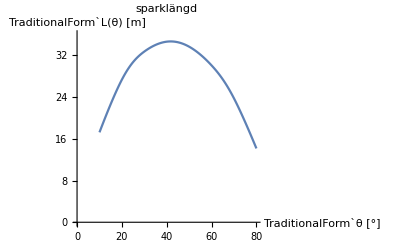

The maximum is computed as

L_max≈35m, θ_max≈41°

## Code

#### Straight Flush

The straight flush can start with possible cards, nine or ten, and can be of four possible suites.

```mathematica
straightFlushC=2^5 Binomial[2, 1] Binomial[4, 1]
```

256

#### Straight

The straight applies same principle above with the exception of flush, no sequence of five suites. 
Binomial[2, 1] = Two possible starting cards, pick one. Binomial[8, 1]=Eight possible suites, including recurrence of same suite, pick one. Repeat five times. Exclude the possibility of flush and straight appearing together.

```mathematica
straightC=Binomial[2, 1] Binomial[8, 1]^5;
straightC - straightFlushC
```

65280

#### Full House

The full house consists of three of kind and a pair of two in the same hand.
Binomial[6, 1]=Pick one out of six possible ranks.Binomial[8, 3]=Pick three out of eight possible suites, including recurrence of same suite.Binomial[5, 1]=Pick one out of the remaining five cards.Binomial[8, 2]=Pick two out of eight possible suites, including recurrence of same suite.

```mathematica
Binomial[6, 1] Binomial[8, 3]Binomial[5, 1]Binomial[8, 2]
```

47040

### Flush

The flush consists of a hand with hand of where all cards holds same suite, but not pair or straight of the rank.
Binomial[12, 5]=Pick five out of the 12 possible suites!!!!!!!!!Binomial[4, 1]=Pick one

```mathematica
flushC=Binomial[12, 5] Binomial[4, 1] ;
flushC-straightFlushC
```

2912

### Four of a kind

```mathematica
Binomial[6, 1] Binomial[8, 4]Binomial[40, 1]
```

16800

### Three of a kind

```mathematica
Binomial[6, 1] Binomial[8, 3]Binomial[5, 2] Binomial[8, 1]^2
```

215040